#### This notebook gets the slow shaper parameters and calibrates its outputs

Need shaper parameters from  Cshaper.nb

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"Cshaper.nb"];
```

```mathematica
Needs["CUDALink`"]
```

Global def of CUDA block dimension.

```mathematica
blockDim = 256;
```

```mathematica
runShaperArgs = {
{"Double",_,"Input"},
{"Double",_,"Input"},
{"Double",_,"Input"},
{"Double",_,"Input"},
"Double",
"Integer32",
"Integer32",
"Integer32",
{"Double",_,"Output"}};
runShaperSource = Import[NotebookDirectory[]<>"PoissonShapers.cu", "Text"];
```

```mathematica
runShaper=CUDAFunctionLoad[runShaperSource,"run_shapers",runShaperArgs,blockDim,"XCompilerInstallation"->"/usr/bin/gcc-8"]
```

CUDAFunction[<>,run_shapers,{{Double,_,Input},{Double,_,Input},{Double,_,Input},{Double,_,Input},Double,Integer32,Integer32,Integer32,{Double,_,Output}}]

```mathematica
nonoise=runShaper[
cout[uModel/.commonValues/.slowValues/.τsub],
cback[uModel/.commonValues/.slowValues/.τsub],
cout[bModel/.commonValues/.slowValues/.τsub],
cback[bModel/.commonValues/.slowValues/.τsub],
0.0,
0,
1,
250,
ConstantArray[0,{1024,250,2}],1024] ;
```

```mathematica
Dimensions[nonoise]
```

{1,1024,250,2}

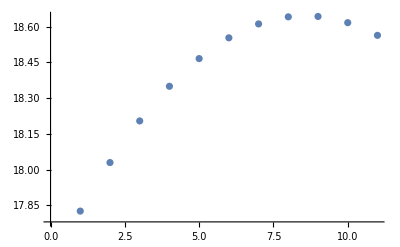

```mathematica
ListPlot[nonoise[[1,1,55;;65,1]]]
```

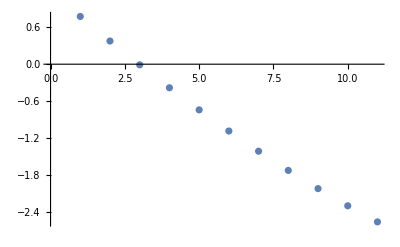

```mathematica
ListPlot[nonoise[[1,1,55;;65,2]]]
```

Peak bipolar response to unit input, for scaling trigger level.

```mathematica
bnorm = Max@@nonoise[[1,1,All,2]]
```

8.89099

```mathematica
eventsArgs = {
{"Double",_,"Input"},
{"Double",_,"Input"},
{"Double",_,"Input"},
{"Double",_,"Input"},
"Double",
"Integer32",
"Double",
"Integer32",
"Double",
{"Double",_,"Output"},
{"Double",_,"Output"},
{"Double",_,"Output"}};
eventsSource = Import[NotebookDirectory[]<>"PoissonEvents.cu", "Text"];
```

```mathematica
events=CUDAFunctionLoad[eventsSource,"events",eventsArgs,blockDim,"XCompilerInstallation"->"/usr/bin/gcc-8"]
```

CUDAFunction[<>,events,{{Double,_,Input},{Double,_,Input},{Double,_,Input},{Double,_,Input},Double,Integer32,Double,Integer32,Double,{Double,_,Output},{Double,_,Output},{Double,_,Output}}]

```mathematica
noNoiseEvents=events[
cout[uModel/.commonValues/.slowValues/.τsub],
cback[uModel/.commonValues/.slowValues/.τsub],
cout[bModel/.commonValues/.slowValues/.τsub],
cback[bModel/.commonValues/.slowValues/.τsub],
0.0,
0,
1,
250,
bnorm/2,
ConstantArray[0,1024],
ConstantArray[0,1024],
ConstantArray[0,1024]
] ;
```

```mathematica
Dimensions[noNoiseEvents]
```

{3,1024}

```mathematica
unorm=noNoiseEvents[[3,1]]
```

18.1994

1 keV in electrons

```mathematica
keV=1000/3.6
```

277.778

```mathematica
tstep = N[τ/.τsub]
```

9.68814×10^-9